This notebook is to study the effect of Gamma of the length distribution for kinetic+rotation+vibration energy.

```mathematica
J=1
A =1
vibration = 1
Timing[Jkrj=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-u×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))-1,{u,-3},MaxIterations->10000],{gamma,{1,10,100,1000,10000}},{x,0.01,15,0.1}]]
```

1

1

1

General::munfl: 175.883/(2039298274118911624692976044998614874707514564867423598278106834085399394«166»2875200268932124981878786621440000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (176.876 89)/(3140720980624160378682208931648383624025948004369661929299574944043649354«170»5196699124005923162587377172480000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (177.87 32041)/(1967912952039486410074698472392244211142178500577942771660527668438869812«175»4773711963133521399878873251840000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{11640.8,{{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352},{13.8056,6.61123,4.92228,4.06873,3.51676,3.11105,2.79056,2.52571,2.3,2.10332,1.92902,1.77249,1.63042,1.50035,1.3804,1.26911,1.1653,1.06804,0.976553,0.890201,0.808445,0.730829,0.656964,0.586512,0.519182,0.454717,0.392893,0.33351,0.27639,0.221374,0.168321,0.117102,0.0676003,0.0197102,-0.0266644,-0.0716115,-0.115212,-0.157539,-0.198662,-0.238643,-0.277542,-0.31541,-0.3523,-0.388258,-0.423326,-0.457546,-0.490956,-0.52359,-0.555484,-0.586666,-0.617168,-0.647016,-0.676237,-0.704855,-0.732893,-0.760373,-0.787316,-0.813741,-0.839667,-0.865111,-0.890091,-0.914621,-0.938717,-0.962394,-0.985665,-1.00854,-1.03104,-1.05317,-1.07494,-1.09636,-1.11745,-1.13821,-1.15866,-1.17879,-1.19863,-1.21817,-1.23744,-1.25642,-1.27514,-1.2936,-1.3118,-1.32976,-1.34747,-1.36495,-1.3822,-1.39922,-1.41603,-1.43262,-1.44901,-1.46519,-1.48117,-1.49696,-1.51256,-1.52797,-1.5432,-1.55825,-1.57313,-1.58784,-1.60239,-1.61677,-1.63099,-1.64505,-1.65896,-1.67272,-1.68634,-1.69981,-1.71314,-1.72633,-1.73938,-1.7523,-1.7651,-1.77776,-1.79029,-1.80271,-1.815,-1.82717,-1.83923,-1.85117,-1.863,-1.87471,-1.88632,-1.89782,-1.90922,-1.92051,-1.9317,-1.94279,-1.95378,-1.96468,-1.97548,-1.98618,-1.99679,-2.00732,-2.01775,-2.0281,-2.03836,-2.04853,-2.05862,-2.06863,-2.07856,-2.0884,-2.09817,-2.10786,-2.11747,-2.12701,-2.13647,-2.14586,-2.15518,-2.16443,-2.17361,-2.18271},{13.8063,7.03275,5.72206,5.00427,4.49947,4.10561,3.78066,3.50307,3.26032,3.04438,2.84983,2.67277,2.51032,2.36027,2.22088,2.09078,1.96884,1.85411,1.74583,1.64334,1.54606,1.45353,1.36531,1.28105,1.20042,1.12314,1.04896,0.977654,0.909022,0.842883,0.779074,0.717448,0.657871,0.600221,0.544386,0.490263,0.437759,0.386788,0.337268,0.289126,0.242294,0.196708,0.152308,0.109039,0.0668508,0.0256939,-0.0144764,-0.0537025,-0.0920239,-0.129478,-0.1661,-0.201923,-0.236977,-0.271293,-0.304899,-0.337819,-0.370081,-0.401706,-0.432718,-0.463137,-0.492985,-0.522279,-0.551039,-0.579282,-0.607024,-0.634282,-0.661069,-0.687402,-0.713293,-0.738756,-0.763803,-0.788447,-0.812699,-0.83657,-0.860071,-0.883211,-0.906002,-0.928452,-0.95057,-0.972365,-0.993845,-1.01502,-1.03589,-1.05648,-1.07678,-1.0968,-1.11655,-1.13604,-1.15527,-1.17425,-1.19299,-1.21148,-1.22974,-1.24777,-1.26557,-1.28316,-1.30053,-1.31769,-1.33465,-1.3514,-1.36796,-1.38432,-1.4005,-1.41649,-1.4323,-1.44794,-1.4634,-1.47868,-1.49381,-1.50876,-1.52356,-1.5382,-1.55268,-1.56702,-1.5812,-1.59524,-1.60913,-1.62289,-1.6365,-1.64998,-1.66332,-1.67654,-1.68962,-1.70258,-1.71542,-1.72813,-1.74072,-1.75319,-1.76555,-1.77779,-1.78992,-1.80194,-1.81385,-1.82566,-1.83736,-1.84895,-1.86045,-1.87184,-1.88313,-1.89433,-1.90543,-1.91644,-1.92735,-1.93818,-1.94891,-1.95955,-1.97011,-1.98058,-1.99096,-2.00127},{13.8135,7.87881,6.75165,6.08002,5.58912,5.19683,4.8672,4.58122,4.32761,4.09908,3.89068,3.69887,3.52102,3.35513,3.19964,3.0533,2.91509,2.78416,2.65981,2.54144,2.42852,2.32061,2.21731,2.11828,2.0232,1.9318,1.84383,1.75907,1.67732,1.59838,1.5221,1.44831,1.37688,1.30768,1.24058,1.17548,1.11227,1.05087,0.991166,0.933095,0.876574,0.821533,0.767905,0.715628,0.664642,0.614893,0.56633,0.518902,0.472566,0.427277,0.382995,0.339682,0.297301,0.255818,0.2152,0.175417,0.136439,0.0982379,0.0607878,0.0240633,-0.0119595,-0.0473033,-0.0819901,-0.11604,-0.149474,-0.182311,-0.214567,-0.246262,-0.277411,-0.30803,-0.338135,-0.367741,-0.39686,-0.425507,-0.453695,-0.481435,-0.508741,-0.535623,-0.562093,-0.588161,-0.613837,-0.639132,-0.664054,-0.688614,-0.71282,-0.736681,-0.760204,-0.783399,-0.806272,-0.828831,-0.851084,-0.873037,-0.894698,-0.916072,-0.937166,-0.957987,-0.97854,-0.998832,-1.01887,-1.03865,-1.05819,-1.07749,-1.09655,-1.11538,-1.13399,-1.15238,-1.17055,-1.1885,-1.20625,-1.22379,-1.24114,-1.25829,-1.27524,-1.29201,-1.30859,-1.32499,-1.34121,-1.35725,-1.37313,-1.38883,-1.40437,-1.41975,-1.43496,-1.45002,-1.46493,-1.47968,-1.49429,-1.50875,-1.52306,-1.53723,-1.55127,-1.56517,-1.57893,-1.59256,-1.60606,-1.61944,-1.63268,-1.64581,-1.65881,-1.67169,-1.68446,-1.69711,-1.70964,-1.72206,-1.73438,-1.74658,-1.75867,-1.77066,-1.78255,-1.79433},{13.8777,8.92888,7.8635,7.2065,6.71979,6.32761,5.9959,5.70639,5.44813,5.21403,4.99923,4.80028,4.61461,4.44027,4.27574,4.11983,3.97156,3.83014,3.6949,3.56529,3.44084,3.32114,3.20585,3.09464,2.98727,2.88347,2.78306,2.68582,2.59159,2.5002,2.41152,2.32542,2.24176,2.16044,2.08135,2.00439,1.92947,1.8565,1.78541,1.71611,1.64854,1.58262,1.51829,1.4555,1.39417,1.33426,1.27572,1.21849,1.16253,1.10779,1.05424,1.00182,0.950502,0.900249,0.851024,0.802793,0.755524,0.709187,0.663751,0.619189,0.575474,0.532579,0.490481,0.449155,0.408579,0.368732,0.329591,0.291137,0.253352,0.216216,0.179711,0.143821,0.108529,0.0738187,0.0396757,0.00608483,-0.026968,-0.0594964,-0.0915137,-0.123033,-0.154065,-0.184624,-0.214719,-0.244363,-0.273566,-0.302339,-0.330691,-0.358632,-0.386172,-0.413319,-0.440084,-0.466473,-0.492496,-0.518161,-0.543475,-0.568446,-0.593081,-0.617388,-0.641374,-0.665045,-0.688408,-0.711469,-0.734234,-0.75671,-0.778902,-0.800817,-0.822459,-0.843834,-0.864948,-0.885805,-0.906411,-0.926769,-0.946886,-0.966766,-0.986413,-1.00583,-1.02503,-1.044,-1.06276,-1.08131,-1.09965,-1.11778,-1.13571,-1.15345,-1.171,-1.18835,-1.20552,-1.2225,-1.2393,-1.25593,-1.27238,-1.28866,-1.30478,-1.32073,-1.33651,-1.35214,-1.36761,-1.38292,-1.39808,-1.4131,-1.42796,-1.44269,-1.45727,-1.4717,-1.48601,-1.50017,-1.5142,-1.52811,-1.54188,-1.55552}}}

```mathematica
x= Range[0.01,15,0.1]
J05 = Jkrj[[1]]
J1 = Jkrj[[2]]
J105 = Jkrj[[3]]
J2 = Jkrj[[4]]
J205=Jkrj[[5]]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01,2.11,2.21,2.31,2.41,2.51,2.61,2.71,2.81,2.91,3.01,3.11,3.21,3.31,3.41,3.51,3.61,3.71,3.81,3.91,4.01,4.11,4.21,4.31,4.41,4.51,4.61,4.71,4.81,4.91,5.01,5.11,5.21,5.31,5.41,5.51,5.61,5.71,5.81,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91}

{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352}

{13.8056,6.61123,4.92228,4.06873,3.51676,3.11105,2.79056,2.52571,2.3,2.10332,1.92902,1.77249,1.63042,1.50035,1.3804,1.26911,1.1653,1.06804,0.976553,0.890201,0.808445,0.730829,0.656964,0.586512,0.519182,0.454717,0.392893,0.33351,0.27639,0.221374,0.168321,0.117102,0.0676003,0.0197102,-0.0266644,-0.0716115,-0.115212,-0.157539,-0.198662,-0.238643,-0.277542,-0.31541,-0.3523,-0.388258,-0.423326,-0.457546,-0.490956,-0.52359,-0.555484,-0.586666,-0.617168,-0.647016,-0.676237,-0.704855,-0.732893,-0.760373,-0.787316,-0.813741,-0.839667,-0.865111,-0.890091,-0.914621,-0.938717,-0.962394,-0.985665,-1.00854,-1.03104,-1.05317,-1.07494,-1.09636,-1.11745,-1.13821,-1.15866,-1.17879,-1.19863,-1.21817,-1.23744,-1.25642,-1.27514,-1.2936,-1.3118,-1.32976,-1.34747,-1.36495,-1.3822,-1.39922,-1.41603,-1.43262,-1.44901,-1.46519,-1.48117,-1.49696,-1.51256,-1.52797,-1.5432,-1.55825,-1.57313,-1.58784,-1.60239,-1.61677,-1.63099,-1.64505,-1.65896,-1.67272,-1.68634,-1.69981,-1.71314,-1.72633,-1.73938,-1.7523,-1.7651,-1.77776,-1.79029,-1.80271,-1.815,-1.82717,-1.83923,-1.85117,-1.863,-1.87471,-1.88632,-1.89782,-1.90922,-1.92051,-1.9317,-1.94279,-1.95378,-1.96468,-1.97548,-1.98618,-1.99679,-2.00732,-2.01775,-2.0281,-2.03836,-2.04853,-2.05862,-2.06863,-2.07856,-2.0884,-2.09817,-2.10786,-2.11747,-2.12701,-2.13647,-2.14586,-2.15518,-2.16443,-2.17361,-2.18271}

{13.8063,7.03275,5.72206,5.00427,4.49947,4.10561,3.78066,3.50307,3.26032,3.04438,2.84983,2.67277,2.51032,2.36027,2.22088,2.09078,1.96884,1.85411,1.74583,1.64334,1.54606,1.45353,1.36531,1.28105,1.20042,1.12314,1.04896,0.977654,0.909022,0.842883,0.779074,0.717448,0.657871,0.600221,0.544386,0.490263,0.437759,0.386788,0.337268,0.289126,0.242294,0.196708,0.152308,0.109039,0.0668508,0.0256939,-0.0144764,-0.0537025,-0.0920239,-0.129478,-0.1661,-0.201923,-0.236977,-0.271293,-0.304899,-0.337819,-0.370081,-0.401706,-0.432718,-0.463137,-0.492985,-0.522279,-0.551039,-0.579282,-0.607024,-0.634282,-0.661069,-0.687402,-0.713293,-0.738756,-0.763803,-0.788447,-0.812699,-0.83657,-0.860071,-0.883211,-0.906002,-0.928452,-0.95057,-0.972365,-0.993845,-1.01502,-1.03589,-1.05648,-1.07678,-1.0968,-1.11655,-1.13604,-1.15527,-1.17425,-1.19299,-1.21148,-1.22974,-1.24777,-1.26557,-1.28316,-1.30053,-1.31769,-1.33465,-1.3514,-1.36796,-1.38432,-1.4005,-1.41649,-1.4323,-1.44794,-1.4634,-1.47868,-1.49381,-1.50876,-1.52356,-1.5382,-1.55268,-1.56702,-1.5812,-1.59524,-1.60913,-1.62289,-1.6365,-1.64998,-1.66332,-1.67654,-1.68962,-1.70258,-1.71542,-1.72813,-1.74072,-1.75319,-1.76555,-1.77779,-1.78992,-1.80194,-1.81385,-1.82566,-1.83736,-1.84895,-1.86045,-1.87184,-1.88313,-1.89433,-1.90543,-1.91644,-1.92735,-1.93818,-1.94891,-1.95955,-1.97011,-1.98058,-1.99096,-2.00127}

{13.8135,7.87881,6.75165,6.08002,5.58912,5.19683,4.8672,4.58122,4.32761,4.09908,3.89068,3.69887,3.52102,3.35513,3.19964,3.0533,2.91509,2.78416,2.65981,2.54144,2.42852,2.32061,2.21731,2.11828,2.0232,1.9318,1.84383,1.75907,1.67732,1.59838,1.5221,1.44831,1.37688,1.30768,1.24058,1.17548,1.11227,1.05087,0.991166,0.933095,0.876574,0.821533,0.767905,0.715628,0.664642,0.614893,0.56633,0.518902,0.472566,0.427277,0.382995,0.339682,0.297301,0.255818,0.2152,0.175417,0.136439,0.0982379,0.0607878,0.0240633,-0.0119595,-0.0473033,-0.0819901,-0.11604,-0.149474,-0.182311,-0.214567,-0.246262,-0.277411,-0.30803,-0.338135,-0.367741,-0.39686,-0.425507,-0.453695,-0.481435,-0.508741,-0.535623,-0.562093,-0.588161,-0.613837,-0.639132,-0.664054,-0.688614,-0.71282,-0.736681,-0.760204,-0.783399,-0.806272,-0.828831,-0.851084,-0.873037,-0.894698,-0.916072,-0.937166,-0.957987,-0.97854,-0.998832,-1.01887,-1.03865,-1.05819,-1.07749,-1.09655,-1.11538,-1.13399,-1.15238,-1.17055,-1.1885,-1.20625,-1.22379,-1.24114,-1.25829,-1.27524,-1.29201,-1.30859,-1.32499,-1.34121,-1.35725,-1.37313,-1.38883,-1.40437,-1.41975,-1.43496,-1.45002,-1.46493,-1.47968,-1.49429,-1.50875,-1.52306,-1.53723,-1.55127,-1.56517,-1.57893,-1.59256,-1.60606,-1.61944,-1.63268,-1.64581,-1.65881,-1.67169,-1.68446,-1.69711,-1.70964,-1.72206,-1.73438,-1.74658,-1.75867,-1.77066,-1.78255,-1.79433}

{13.8777,8.92888,7.8635,7.2065,6.71979,6.32761,5.9959,5.70639,5.44813,5.21403,4.99923,4.80028,4.61461,4.44027,4.27574,4.11983,3.97156,3.83014,3.6949,3.56529,3.44084,3.32114,3.20585,3.09464,2.98727,2.88347,2.78306,2.68582,2.59159,2.5002,2.41152,2.32542,2.24176,2.16044,2.08135,2.00439,1.92947,1.8565,1.78541,1.71611,1.64854,1.58262,1.51829,1.4555,1.39417,1.33426,1.27572,1.21849,1.16253,1.10779,1.05424,1.00182,0.950502,0.900249,0.851024,0.802793,0.755524,0.709187,0.663751,0.619189,0.575474,0.532579,0.490481,0.449155,0.408579,0.368732,0.329591,0.291137,0.253352,0.216216,0.179711,0.143821,0.108529,0.0738187,0.0396757,0.00608483,-0.026968,-0.0594964,-0.0915137,-0.123033,-0.154065,-0.184624,-0.214719,-0.244363,-0.273566,-0.302339,-0.330691,-0.358632,-0.386172,-0.413319,-0.440084,-0.466473,-0.492496,-0.518161,-0.543475,-0.568446,-0.593081,-0.617388,-0.641374,-0.665045,-0.688408,-0.711469,-0.734234,-0.75671,-0.778902,-0.800817,-0.822459,-0.843834,-0.864948,-0.885805,-0.906411,-0.926769,-0.946886,-0.966766,-0.986413,-1.00583,-1.02503,-1.044,-1.06276,-1.08131,-1.09965,-1.11778,-1.13571,-1.15345,-1.171,-1.18835,-1.20552,-1.2225,-1.2393,-1.25593,-1.27238,-1.28866,-1.30478,-1.32073,-1.33651,-1.35214,-1.36761,-1.38292,-1.39808,-1.4131,-1.42796,-1.44269,-1.45727,-1.4717,-1.48601,-1.50017,-1.5142,-1.52811,-1.54188,-1.55552}

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.692] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

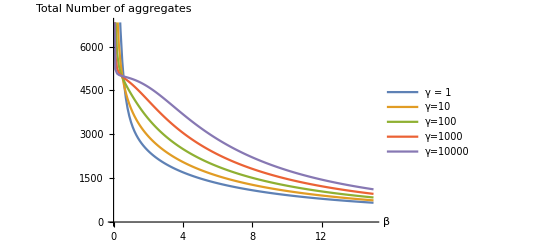

```mathematica
ListLinePlot[{(ⅇ^-J05+1×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J05+1×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J1+10×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J1+10×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J105+100×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J105+100×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J2+1000×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J2+1000×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000,
(ⅇ^-J205+10000×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J205+10000×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))×10000},DataRange->{0,15},PlotLegends->{"γ = 1","γ=10","γ=100","γ=1000","γ=10000"},AxesLabel->{"β","Total Number of aggregates"}]
```

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.692] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

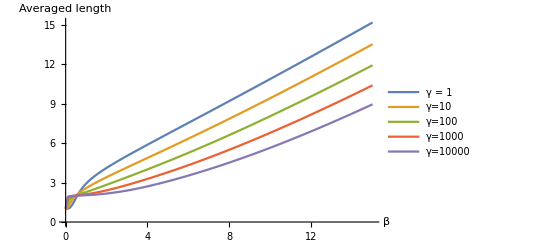

```mathematica
ListLinePlot[{(ⅇ^-J05+1×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J05+1×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J1+10×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J1+10×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J105+100×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J105+100×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),(ⅇ^-J2+1000×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J2+1000×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)])),
(ⅇ^-J205+10000×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))/(ⅇ^-J205+10000×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))},DataRange->{0,15},PlotLegends->{"γ = 1","γ=10","γ=100","γ=1000","γ=10000"},AxesLabel->{"β","Averaged length"}]
```